```mathematica
Get["BDetSpread/Definitions.m"]
```

```mathematica
Get["TransportFunctions/XDataCreation.m"];
```

```mathematica
XDatam55p05Bins32=XDataCreation[{-0.055,0.005},32]
```

{-0.055,-0.0530645,-0.051129,-0.0491935,-0.0472581,-0.0453226,-0.0433871,-0.0414516,-0.0395161,-0.0375806,-0.0356452,-0.0337097,-0.0317742,-0.0298387,-0.0279032,-0.0259677,-0.0240323,-0.0220968,-0.0201613,-0.0182258,-0.0162903,-0.0143548,-0.0124194,-0.0104839,-0.00854839,-0.0066129,-0.00467742,-0.00274194,-0.000806452,0.00112903,0.00306452,0.005}

### memoization

```mathematica
ClearAll[FitFuncMemoArith]
```

```mathematica
FitFuncMemoDetSpreadArith[
{b_,alpha_,BRxB_,rRxB_,rD_,rF_,rA_},{xA_,yA_,xOff_,yOff_,y0_},XList_,IntPrec_
]:=
FitFuncMemoDetSpreadArith[{b,alpha,BRxB,rRxB,rD,rF,rA},{xA,yA,xOff,yOff,y0},XList,IntPrec]=
Reverse[IntTableDetSpreadArith[{b,alpha,BRxB,rRxB,rD,rF,rA},{xA,yA,xOff,yOff,y0},XList,IntPrec]]
```

### bin selection and normalization

```mathematica
FitFuncBinNormDetSpreadArith[bin_?NumericQ,{b_?NumericQ,alpha_?NumericQ,BRxB_?NumericQ,rRxB_?NumericQ,rD_?NumericQ,rF_?NumericQ,rA_},{xA_,yA_,xOff_,yOff_,y0_},XList_,IntPrec_]:=FitFuncMemoDetSpreadArith[{b,alpha,BRxB,rRxB,rD,rF,rA},{xA,yA,xOff,yOff,y0},XList,IntPrec][[bin]]/Total[FitFuncMemoDetSpreadArith[{b,alpha,BRxB,rRxB,rD,rF,rA},{xA,yA,xOff,yOff,y0},XList,IntPrec]]
```

Data 90° no Filter

```mathematica
t0=AbsoluteTime[];
ILLData90noFilter=Table[{bin,FitFuncBinNormDetSpreadArith[bin,{0.,Pi/2,0.2,1./2,1./2,1.,1/2.},{0.01,0.035,0.,0.,0.},XDatam55p05Bins32,3]},{bin,1,Length[XDatam55p05Bins32]}];
t1=AbsoluteTime[];
t1-t0
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33401 and 0.00487771 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14544 and 0.00554642 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.0346 and 0.00895122 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4563 and 0.015101 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4627 and 0.0271419 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8615 and 0.0155815 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3624 and 0.0104235 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94809 and 0.00517473 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72955 and 0.0121513 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06116 and 0.0367431 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172851 and 0.000378845 for the integral and error estimates.

510.745854

### 510s

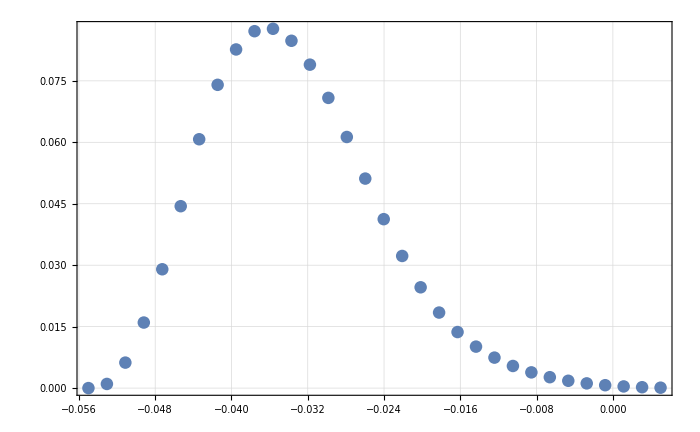

```mathematica
ListPlot[Transpose[{XDatam55p05Bins32,ILLData90noFilter[[All,2]]}]]
```

Fits

### drD fit

```mathematica
t0=AbsoluteTime[];
Print[DateString[]]
drDFit=Reap[NonlinearModelFit[
ILLData90noFilter,
{
FitFuncBinNormDetSpreadArith[bin,{b,Pi/2,0.2,1./2,1./2+1/2*10^-4,1.,1/2.},{0.01,0.035,0.,0.,0.},XDatam55p05Bins32,3],
-0.002<b<0.002
},
{{b,0.0001}},bin,MaxIterations->6,EvaluationMonitor:>Sow[b],Method->"NMinimize",PrecisionGoal->5,AccuracyGoal->6
]
];
t1=AbsoluteTime[];
t1-t0
```

Mon 1 Jul 2019 17:39:42

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33349 and 0.00490071 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14481 and 0.00555129 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03385 and 0.00900082 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4558 and 0.0153127 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4633 and 0.026873 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8625 and 0.0157702 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3635 and 0.0104205 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94858 and 0.00517799 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72977 and 0.0121562 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06123 and 0.0367644 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.17283 and 0.000378118 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.3341 and 0.00490232 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.1456 and 0.00545082 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03523 and 0.0092398 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4573 and 0.0152093 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4636 and 0.0268716 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8615 and 0.0157687 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3614 and 0.0108624 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94716 and 0.00517706 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72886 and 0.0121532 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06079 and 0.0367553 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172736 and 0.000377901 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33415 and 0.00490244 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14565 and 0.00545096 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03534 and 0.00923992 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4574 and 0.0152095 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4637 and 0.0268715 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8614 and 0.0157686 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3612 and 0.0108623 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94706 and 0.00517698 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72879 and 0.012153 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06075 and 0.0367546 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172729 and 0.000377884 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33407 and 0.00490224 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14556 and 0.00545074 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03517 and 0.00923972 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4572 and 0.0152756 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4636 and 0.0268717 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8615 and 0.0157688 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3615 and 0.0108624 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94723 and 0.0051771 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.7289 and 0.0121534 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06081 and 0.0367557 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.17274 and 0.000377911 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.3336 and 0.004901 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14495 and 0.00555161 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.0341 and 0.00900112 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.456 and 0.015313 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4634 and 0.0268728 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8623 and 0.0157699 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3631 and 0.0104203 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94833 and 0.00517782 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06115 and 0.0367627 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.7296 and 0.0121556 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172813 and 0.000378079 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33408 and 0.00490226 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14557 and 0.00545076 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03519 and 0.00923974 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4573 and 0.0152756 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4636 and 0.0268716 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8615 and 0.0157688 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3614 and 0.0108624 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94721 and 0.00517709 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72889 and 0.0121533 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.0608 and 0.0367556 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172739 and 0.000377908 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33295 and 0.00489928 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14412 and 0.00554971 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03261 and 0.0090419 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4545 and 0.015311 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.463 and 0.0268743 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8635 and 0.0157715 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3654 and 0.0104236 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94984 and 0.00517882 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.73057 and 0.0121588 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06161 and 0.0367725 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172913 and 0.000378312 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.3341 and 0.0049023 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14559 and 0.00545081 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03522 and 0.00923979 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4573 and 0.0152757 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4636 and 0.0268716 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8615 and 0.0157687 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3614 and 0.0108624 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94718 and 0.00517706 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72887 and 0.0121532 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06079 and 0.0367553 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172737 and 0.000377902 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33318 and 0.00489988 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.1444 and 0.00555037 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03288 and 0.00924792 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.455 and 0.0153117 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4632 and 0.0268738 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8631 and 0.0157709 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3646 and 0.010421 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94932 and 0.00517848 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.73024 and 0.0121577 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06145 and 0.0367691 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172879 and 0.000378231 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33291 and 0.00489916 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14406 and 0.00554958 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.0325 and 0.00904178 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4544 and 0.0153109 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.463 and 0.0268744 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8635 and 0.0157716 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3656 and 0.0104237 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94995 and 0.00517889 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.73064 and 0.012159 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06165 and 0.0367732 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172921 and 0.000378328 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.3341 and 0.00490232 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.1456 and 0.00545082 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03523 and 0.0092398 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4573 and 0.0152093 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4636 and 0.0268716 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8615 and 0.0157687 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3614 and 0.0108624 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94716 and 0.00517706 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72886 and 0.0121532 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06079 and 0.0367553 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172736 and 0.000377901 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33311 and 0.0048997 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14432 and 0.00555018 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03274 and 0.00924775 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4549 and 0.0153115 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4631 and 0.026874 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8632 and 0.0157711 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3649 and 0.0104234 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94947 and 0.00517858 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.73034 and 0.012158 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.0615 and 0.0367701 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172889 and 0.000378255 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33362 and 0.00490105 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14497 and 0.00555166 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03414 and 0.00900117 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4561 and 0.015313 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4634 and 0.0268727 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8623 and 0.0157699 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.363 and 0.0104203 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94829 and 0.0051778 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72958 and 0.0121556 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06113 and 0.0367625 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.17281 and 0.000378073 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33349 and 0.0049007 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.1448 and 0.00555127 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03384 and 0.0090008 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4558 and 0.0153126 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4633 and 0.0268731 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8625 and 0.0157702 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3635 and 0.0104205 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94859 and 0.005178 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72977 and 0.0121562 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06123 and 0.0367645 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172831 and 0.00037812 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33406 and 0.0049022 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14554 and 0.0054507 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03514 and 0.00923968 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4572 and 0.0152756 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4636 and 0.0268717 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8615 and 0.0157688 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3615 and 0.0108625 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94727 and 0.00517712 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06082 and 0.0367559 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72892 and 0.0121534 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172743 and 0.000377916 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33416 and 0.00490248 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14567 and 0.005451 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03537 and 0.00923996 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4574 and 0.0152095 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4637 and 0.0268714 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8614 and 0.0157686 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3611 and 0.0108623 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94702 and 0.00517696 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72877 and 0.0121529 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06074 and 0.0367544 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172727 and 0.000377879 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33354 and 0.00490082 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14486 and 0.00555141 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03394 and 0.00900093 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4559 and 0.0153128 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4633 and 0.0268729 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8625 and 0.0157701 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3634 and 0.0104204 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94849 and 0.00517793 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72971 and 0.012156 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.0612 and 0.0367638 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172824 and 0.000378104 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33298 and 0.00489935 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14415 and 0.00554979 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03244 and 0.0092474 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4545 and 0.0153111 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4631 and 0.0268743 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8634 and 0.0157714 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3654 and 0.0104236 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94978 and 0.00517878 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.73053 and 0.0121587 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06159 and 0.0367721 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172909 and 0.000378302 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33382 and 0.00490157 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14524 and 0.00545002 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03459 and 0.00900172 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4566 and 0.0152748 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4635 and 0.0268723 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.862 and 0.0157694 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3623 and 0.01042 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94782 and 0.00517749 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72928 and 0.0121546 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06099 and 0.0367595 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172779 and 0.000378001 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33288 and 0.00489909 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14403 and 0.0055495 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03244 and 0.00904171 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4543 and 0.0153108 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.463 and 0.0268745 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8636 and 0.0157716 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3657 and 0.0104237 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.95001 and 0.00517893 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.73068 and 0.0121592 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06167 and 0.0367736 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172925 and 0.000378338 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33392 and 0.00490184 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14536 and 0.0054503 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03481 and 0.00900199 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4569 and 0.0152751 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4635 and 0.026872 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8618 and 0.0157691 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.362 and 0.0104198 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94759 and 0.00517734 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06092 and 0.036758 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72913 and 0.0121541 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172764 and 0.000377966 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33333 and 0.00490028 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.1446 and 0.00555081 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03348 and 0.00900037 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4554 and 0.0153122 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4632 and 0.0268734 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8628 and 0.0157706 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3641 and 0.0104208 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94896 and 0.00517824 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.73001 and 0.012157 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06134 and 0.0367668 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172855 and 0.000378176 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33326 and 0.00490009 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.1445 and 0.0055506 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03332 and 0.00900016 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4552 and 0.0153119 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4632 and 0.0268736 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8629 and 0.0157707 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3644 and 0.0104209 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94913 and 0.00517836 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.0614 and 0.036768 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.73012 and 0.0121573 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172867 and 0.000378203 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33405 and 0.00490219 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14554 and 0.00545069 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03513 and 0.00923968 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4572 and 0.0152756 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4636 and 0.0268717 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8615 and 0.0157688 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3615 and 0.0108625 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94727 and 0.00517713 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72893 and 0.0121534 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06082 and 0.036756 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172743 and 0.000377917 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33341 and 0.00490048 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.1447 and 0.00555103 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03365 and 0.00900057 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4556 and 0.0153124 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4633 and 0.0268733 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8627 and 0.0157704 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3638 and 0.0104207 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94879 and 0.00517813 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.7299 and 0.0121566 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06129 and 0.0367657 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172843 and 0.00037815 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.3339 and 0.0049018 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14534 and 0.00545026 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03478 and 0.00900195 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4568 and 0.0152751 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4635 and 0.0268721 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8618 and 0.0157692 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.362 and 0.0104198 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94762 and 0.00517736 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06093 and 0.0367582 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72915 and 0.0121542 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172766 and 0.000377971 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33413 and 0.00490238 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14563 and 0.00545089 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03529 and 0.00923987 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4573 and 0.0152094 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4637 and 0.0268715 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8614 and 0.0157687 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3613 and 0.0108623 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94711 and 0.00517702 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72882 and 0.0121531 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06077 and 0.0367549 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172732 and 0.000377892 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33413 and 0.0049024 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14564 and 0.00545091 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03531 and 0.00923988 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4573 and 0.0152094 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4637 and 0.0268715 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8614 and 0.0157686 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3612 and 0.0108623 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94709 and 0.00517701 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06077 and 0.0367548 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72881 and 0.0121531 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172731 and 0.000377889 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33389 and 0.00490176 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14533 and 0.00545022 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03475 and 0.00900191 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4568 and 0.0152751 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4635 and 0.0268721 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8618 and 0.0157692 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3621 and 0.0104198 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94765 and 0.00517738 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72917 and 0.0121542 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06094 and 0.0367584 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172768 and 0.000377976 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33409 and 0.00490228 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14558 and 0.00545078 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.0352 and 0.00923976 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4573 and 0.0152757 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4636 and 0.0268716 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8615 and 0.0157687 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3614 and 0.0108624 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.9472 and 0.00517708 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72888 and 0.0121533 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.0608 and 0.0367555 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172738 and 0.000377906 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33375 and 0.00490139 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14514 and 0.00555204 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03443 and 0.00900153 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4565 and 0.0152746 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4635 and 0.0268724 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8621 and 0.0157696 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3626 and 0.0104201 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06104 and 0.0367605 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94798 and 0.00517759 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72938 and 0.0121549 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.17279 and 0.000378026 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33406 and 0.00490222 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14555 and 0.00545072 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03515 and 0.0092397 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4572 and 0.0152756 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4636 and 0.0268717 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8615 and 0.0157688 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3615 and 0.0108625 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94725 and 0.00517711 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72892 and 0.0121534 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06081 and 0.0367558 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172742 and 0.000377914 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33395 and 0.00490193 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14541 and 0.0054504 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.0349 and 0.00923941 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.457 and 0.0152752 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4636 and 0.0268719 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8617 and 0.0157691 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3618 and 0.0104197 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94751 and 0.00517728 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72908 and 0.0121539 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06089 and 0.0367575 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172759 and 0.000377954 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33374 and 0.00490135 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14512 and 0.005552 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.0344 and 0.00900149 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4564 and 0.0152746 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4635 and 0.0268725 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8621 and 0.0157696 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3626 and 0.0104201 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94801 and 0.00517762 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06105 and 0.0367607 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.7294 and 0.012155 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172792 and 0.000378031 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33365 and 0.00490112 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.145 and 0.00555173 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.0342 and 0.00900124 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4562 and 0.0153131 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4634 and 0.0268727 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8623 and 0.0157698 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.363 and 0.0104203 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94822 and 0.00517776 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72954 and 0.0121554 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06111 and 0.0367621 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172806 and 0.000378063 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33323 and 0.00490002 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14447 and 0.00555052 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03301 and 0.00924806 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4552 and 0.0153118 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4632 and 0.0268737 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.863 and 0.0157708 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3644 and 0.010421 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94919 and 0.00517839 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.73016 and 0.0121575 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06141 and 0.0367683 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.17287 and 0.000378212 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33368 and 0.00490121 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14505 and 0.00555184 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03428 and 0.00900133 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4562 and 0.0153132 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4634 and 0.0268726 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8622 and 0.0157697 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3628 and 0.0104202 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94814 and 0.0051777 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72949 and 0.0121553 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06109 and 0.0367616 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172801 and 0.000378051 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33347 and 0.00490065 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14478 and 0.00555122 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03379 and 0.00900075 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4557 and 0.0153126 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4633 and 0.0268731 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8626 and 0.0157702 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3636 and 0.0104206 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94864 and 0.00517803 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.7298 and 0.0121563 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06124 and 0.0367648 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172834 and 0.000378127 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33356 and 0.00490089 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14489 and 0.00555149 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.034 and 0.009001 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4559 and 0.0153129 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4634 and 0.0268729 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8624 and 0.01577 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3633 and 0.0104204 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94842 and 0.00517789 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72966 and 0.0121558 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06118 and 0.0367634 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172819 and 0.000378094 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33382 and 0.00490157 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14524 and 0.00545002 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03459 and 0.00900172 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4566 and 0.0152748 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4635 and 0.0268723 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.862 and 0.0157694 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3623 and 0.01042 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94782 and 0.00517749 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72928 and 0.0121546 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06099 and 0.0367595 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172779 and 0.000378001 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33382 and 0.00490157 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14524 and 0.00545002 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03459 and 0.00900172 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4566 and 0.0152748 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4635 and 0.0268723 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.862 and 0.0157694 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3623 and 0.01042 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94782 and 0.00517749 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72928 and 0.0121546 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06099 and 0.0367595 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172779 and 0.000378001 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33382 and 0.00490157 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14524 and 0.00545002 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03459 and 0.00900172 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4566 and 0.0152748 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4635 and 0.0268723 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.862 and 0.0157694 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3623 and 0.01042 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94782 and 0.00517749 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72928 and 0.0121546 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06099 and 0.0367595 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172779 and 0.000378001 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.89713 and 0.00373479 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.58612 and 0.00401948 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.64543 and 0.010002 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 6.04542 and 0.00818211 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.40166 and 0.0138846 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.8362 and 0.0150858 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.2352 and 0.0284775 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 15.6252 and 0.0166665 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.9683 and 0.00854892 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.38236 and 0.0148182 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.37585 and 0.0427142 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.240452 and 0.000534165 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.89713 and 0.00373479 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.58612 and 0.00401948 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.64543 and 0.010002 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 6.04542 and 0.00818211 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.40166 and 0.0138846 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.8362 and 0.0150858 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.2352 and 0.0284775 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 15.6252 and 0.0166665 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.9683 and 0.00854892 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.38236 and 0.0148182 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.37585 and 0.0427142 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.240452 and 0.000534165 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33382 and 0.00490157 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14524 and 0.00545002 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03459 and 0.00900172 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4566 and 0.0152748 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4635 and 0.0268723 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.862 and 0.0157694 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3623 and 0.01042 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94782 and 0.00517749 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72928 and 0.0121546 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06099 and 0.0367595 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172779 and 0.000378001 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33382 and 0.00490157 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14524 and 0.00545002 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03459 and 0.00900172 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4566 and 0.0152748 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4635 and 0.0268723 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.862 and 0.0157694 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3623 and 0.01042 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94782 and 0.00517749 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72928 and 0.0121546 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06099 and 0.0367595 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172779 and 0.000378001 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.94808 and 0.00387148 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.6514 and 0.00416852 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.74529 and 0.0102628 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.16061 and 0.00820653 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 9.5251 and 0.0142314 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.2625 and 0.0281273 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 15.5362 and 0.0166171 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.84917 and 0.00839432 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.33908 and 0.0420831 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.30631 and 0.0144514 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.23255 and 0.000517658 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.94808 and 0.00387148 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.6514 and 0.00416852 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.74529 and 0.0102628 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.16061 and 0.00820653 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 9.5251 and 0.0142314 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.2625 and 0.0281273 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 15.5362 and 0.0166171 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.84917 and 0.00839432 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.30631 and 0.0144514 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.33908 and 0.0420831 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.23255 and 0.000517658 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33382 and 0.00490157 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14524 and 0.00545002 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03459 and 0.00900172 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4566 and 0.0152748 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4635 and 0.0268723 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.862 and 0.0157694 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3623 and 0.01042 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94782 and 0.00517749 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06099 and 0.0367595 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72928 and 0.0121546 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172779 and 0.000378001 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33382 and 0.00490157 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14524 and 0.00545002 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03459 and 0.00900172 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4566 and 0.0152748 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4635 and 0.0268723 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.862 and 0.0157694 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3623 and 0.01042 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94782 and 0.00517749 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72928 and 0.0121546 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06099 and 0.0367595 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172779 and 0.000378001 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.3338 and 0.00490152 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14521 and 0.00544996 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03454 and 0.00900166 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4566 and 0.0152748 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4635 and 0.0268723 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.862 and 0.0157694 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3624 and 0.01042 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94787 and 0.00517752 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72931 and 0.0121547 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06101 and 0.0367598 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172783 and 0.000378009 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.3338 and 0.00490152 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14521 and 0.00544996 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03454 and 0.00900166 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4566 and 0.0152748 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4635 and 0.0268723 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.862 and 0.0157694 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3624 and 0.01042 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94787 and 0.00517752 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72931 and 0.0121547 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06101 and 0.0367598 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172783 and 0.000378009 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.3338 and 0.00490151 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14521 and 0.00544995 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03454 and 0.00900165 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4566 and 0.0152748 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4635 and 0.0268723 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.862 and 0.0157694 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3624 and 0.01042 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94787 and 0.00517752 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06101 and 0.0367598 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72931 and 0.0121547 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172783 and 0.00037801 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.3338 and 0.00490151 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14521 and 0.00544995 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03454 and 0.00900165 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4566 and 0.0152748 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4635 and 0.0268723 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.862 and 0.0157694 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3624 and 0.01042 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94787 and 0.00517752 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72931 and 0.0121547 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06101 and 0.0367598 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172783 and 0.00037801 for the integral and error estimates.

24858.24408

### took 24858s or 6.9h

```mathematica
drDFit[[1]]["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
b | -0.000818071 | 0.0000910504 | -8.98481 | 3.87318×10^-10

```mathematica
drDFit[[1]]["BestFitParameters"][[1,2]]/10^-4
```

-8.18071

now with offset so that det is around zero, should change behaviour

```mathematica
OffsetXDatam55p05Bins32=Table[x,{x,-0.055+0.025,0.005+0.025,0.06/(32-1)}]
```

{-0.03,-0.0280645,-0.026129,-0.0241935,-0.0222581,-0.0203226,-0.0183871,-0.0164516,-0.0145161,-0.0125806,-0.0106452,-0.00870968,-0.00677419,-0.00483871,-0.00290323,-0.000967742,0.000967742,0.00290323,0.00483871,0.00677419,0.00870968,0.0106452,0.0125806,0.0145161,0.0164516,0.0183871,0.0203226,0.0222581,0.0241935,0.026129,0.0280645,0.03}

```mathematica
t0=AbsoluteTime[];
OffsetILLData90noFilter=Table[{bin,FitFuncBinNormDetSpreadArith[bin,{0.,Pi/2,0.2,1./2,1./2,1.,1/2.},{0.01,0.035,0.025,0.,0.},OffsetXDatam55p05Bins32,3]},{bin,1,Length[OffsetXDatam55p05Bins32]}];
t1=AbsoluteTime[];
t1-t0
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33401 and 0.00487771 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14544 and 0.00554641 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.0346 and 0.0089512 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4563 and 0.0151011 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4627 and 0.0271421 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8615 and 0.0155815 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3624 and 0.0104243 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94809 and 0.00517484 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72955 and 0.0121514 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06116 and 0.0367432 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172851 and 0.000378797 for the integral and error estimates.

513.584752

### 510s

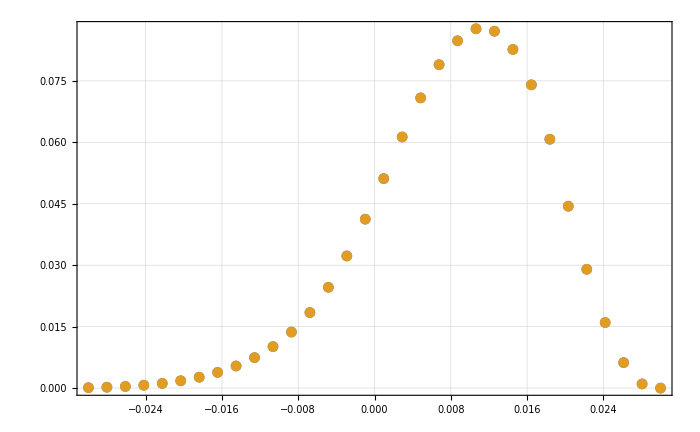

```mathematica
ListPlot[{
Transpose[{Reverse[OffsetXDatam55p05Bins32],OffsetILLData90noFilter[[All,2]]}],
Transpose[{Reverse[XDatam55p05Bins32+0.025],ILLData90noFilter[[All,2]]}]
}]
```

### so yeah, its really just the same data, just shifted. but systematic effects now will be different!

### drD fit

```mathematica
t0=AbsoluteTime[];
Print[DateString[]]
drDFitOffset=Reap[NonlinearModelFit[
OffsetILLData90noFilter,
{
FitFuncBinNormDetSpreadArith[bin,{b,Pi/2,0.2,1./2,1./2+1/2*10^-4,1.,1/2.},{0.01,0.035,0.025,0.,0.},OffsetXDatam55p05Bins32,3],
-0.002<b<0.002
},
{{b,0.0001}},bin,MaxIterations->6,EvaluationMonitor:>Sow[b],Method->"NMinimize",PrecisionGoal->5,AccuracyGoal->6
]
];
t1=AbsoluteTime[];
t1-t0
```

Tue 2 Jul 2019 14:23:01

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33395 and 0.00491364 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14542 and 0.00543934 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03484 and 0.00895131 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4568 and 0.0150539 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4639 and 0.0270946 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8624 and 0.0154523 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3617 and 0.0104554 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94701 and 0.00511432 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72856 and 0.0121179 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06061 and 0.0367704 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172559 and 0.0003772 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33456 and 0.00491525 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14619 and 0.00545236 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03621 and 0.00895297 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4582 and 0.0150557 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4643 and 0.0271432 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8613 and 0.015451 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3596 and 0.0104203 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94559 and 0.00511332 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72766 and 0.0121067 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06017 and 0.0367613 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172465 and 0.000376982 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33461 and 0.00491538 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14625 and 0.0054525 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03632 and 0.0089531 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4584 and 0.0150559 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4643 and 0.027143 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8612 and 0.0154509 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3594 and 0.0104202 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94549 and 0.00511325 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72759 and 0.0121065 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06014 and 0.0367606 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172458 and 0.000376966 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33453 and 0.00491518 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14616 and 0.00545228 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03615 and 0.00895289 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4582 and 0.0150557 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4643 and 0.0271432 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8614 and 0.015451 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3597 and 0.0104204 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94566 and 0.00511337 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06019 and 0.0367617 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.7277 and 0.0121069 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.17247 and 0.000376993 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

### took 24858s or 6.9h

```mathematica
drDFitOffset[[1]]["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
b | -0.000818071 | 0.0000910504 | -8.98481 | 3.87318×10^-10

```mathematica
drDFitOffset[[1]]["BestFitParameters"][[1,2]]/10^-4
```

-8.18071